## Tutorial: Supercells, accessing supercell sequneces

This is a notebook for the first steps for the use of the HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices.

## Preliminaries:

### Remark:

Before using the getting started with the HyperBloch notebook:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website (link to website ???).

Make sure that the required files .hcm and .hcs files are in the current directory. This entails files:

{8,8}-tess_T2.6_3.hcm

{8,8}-tess_T2.6_3_sc-T3.11.hcs

{8,8}-tess_T2.6_3_sc-T5.13.hcs

{8,8}-tess_T2.6_3_sc-T9.20.hcs

{8,8}-tess_T2.6_3_sc-T17.29.hcs

{8,8}-tess_T2.6_3_sc-T33.44.hcs

{8,8}-tess_T2.6_3_sc-T65.78.hcs

In case no such files exists, please follow the instructions in the the prerequisites section on the website (link to website ???) or download it there.

### Load the HyperBloch package:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Open the documentation:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

## First supercell sequence:

### Import cells

We first import the cell, model, and supercell model graphs as produced by the HyperCells package:

Primitive cell:

```mathematica
pcmodel=ImportModelGraphString[Import[FileNameJoin[{"data","cells","{8,8}-tess_T2.6_3.hcm"}]]];
```

Supercells:

```mathematica
scmodels=Association[#->
ImportSupercellModelGraphString[ 
Import@FileNameJoin[{"data","cells",ToString@StringForm["{8,8}-tess_T2.6_3_sc-``.hcs",#]}]]
&/@cells[[2;;]]];
```

We consider the following sequence of supercells, defined in terms of quotients given in https://www.math.auckland.ac.nz/~conder/TriangleGroupQuotients101.txt by M. Conder, (the cell “T2.6” is the primitive cell):

```mathematica
cells={"T2.6","T3.11","T5.13","T9.20","T17.29","T33.44","T65.78"}; 
genusLst={2,3,5,9,17,33,65};
```

### Hamiltonian:

Primitive cell:

The Hamiltonian for the nearest-neighbor tight-binding model on the primitive cell T2.6 is:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,0&,-1&];
```

Supercells:

The Hamiltonians for the nearest - neighbor tight - binding model on the sequence of supercells are, (this might take a minute):

```mathematica
Hclst=
Join[Association["T2.6"->Hpc],
Association[#->
AbelianBlochHamiltonian[scmodels[#],1,0&,-1&,PCModel->pcmodel,CompileFunction->True]
&/@supercells]];
```

### Density of states:

Let us compute the density of states by exact diagonalization:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},2genus]],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

Compute the Eigenvalues via 5·10^4 momentum random samples, (this might take a minute):

```mathematica
evals=Association[cells[[#]]->ComputeEigenvalues[Hclst[cells[[#]]], 5 10^4,32,genusLst[[#]]]&/@Range[7]];
```

Visualize density of states via a kernel density estimation, (this might take a minute):

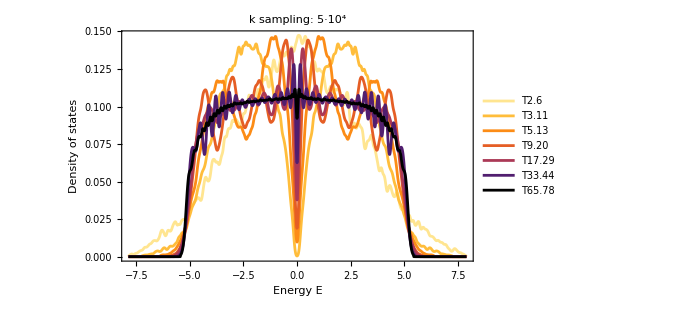

```mathematica
SmoothHistogram[evals,0.05,"PDF",Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->All, LabelStyle->20,PlotLabel->"k sampling: 5·10^4",PlotStyle->(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,7]/7.)),ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},Background->None]
```

```mathematica
NotebookSave[]
```